```mathematica
SetDirectory[NotebookDirectory[]];
$PrePrint=StandardForm;
```

## Loading the data

```mathematica
$DataPath = "precalculated_data";
$FiguresPath = "figures";
```

```mathematica
(* Load helper functions *)
<<CrossSection`
(* Load Kiselev's cross sections (corrected for PV state) *)
<<TreeLevelKnownCrossSections`

nb = 0.3894 10^6;
pb =10^3 nb;
fb =10^6 nb;
μb =10^-3 nb;
$fBc=0.4;
(*mb =10^-6 nb;*)
AllStates = {"PP","PV", "VV"};
zAllStates = {"zPP","zPV", "zVV"};
AllStatesWithZ = Join[AllStates,zAllStates];
$ecmMin = √($SMIN);
toR[x_]:=x/.MC->r M/.MB->(1-r)M/.s->s M^2;
```

Package-X v1.0.4, by Hiren H. Patel

For more information, see the

```mathematica
(*Get["/Users/poslavsky/Projects/Mathematica/AlekhinPDF/Alekhin/a02m.m"]
seta02m["/Users/poslavsky/Projects/Mathematica/AlekhinPDF/Alekhin/",2,0]
Export[ToFileName[$DataPath,"alphaS.m"],Compress[Table[{e,alphas[e^2]},{e,√(a02m`Private`qsqmin),10$ecmMax,0.1}]]]*)
```

```mathematica
(* Loading strong couling AlphaS[scale] *)
Clear[$AlphaS]
$AlphaS = Interpolation[Uncompress@Import[ToFileName[$DataPath,"alphaS.m"]]];
AlphaS[x_/;NumberQ[x]]:=$AlphaS[x]
```

```mathematica
$ΛQCD=0.2;
AlphaS1Loop[x_,ΛQCD_]:=(2π)/((11-(2/3) 6)Log[x/ΛQCD])
AlphaS1Loop[x_]:=AlphaS1Loop[x,$ΛQCD]
$ΛQCDatMZ=NSolve[AlphaS1Loop[$MZ,x]==0.1184,x,Reals][[1,1,2]];
AlphaS1LoopMZ[x_]:=AlphaS1Loop[x,$ΛQCDatMZ]
```

```mathematica
CosIntegrate[expr_]:=Module[{tmp,res},
If[!PolynomialQ[expr,cos],Throw["Not a polynomial: "<>ToString[InputForm@expr]]];
tmp = CoefficientList[expr,cos];
res = 0;
Do[
res  = res + tmp[[i]](1^(i)-(-1)^(i))/(i);
,{i,1,Length[tmp]}];
res
]
CosIntegrate[expr_List]:=CosIntegrate/@expr;
```

```mathematica
(* Load analytical tree level cross sections *) 
(DsDCosThetaTree[#]=Import[ToFileName[$DataPath,#<>"DsDCosThetaTree.m"]];CrossSectionTree[#]=Import[ToFileName[$DataPath,#<>"CrossSectionTree.m"]];)&/@AllStatesWithZ;
```

```mathematica
(* Check that for gamma results are equal to Kiselev *)
(FullSimplify@Factor[DsDCosThetaTree[#]-$Kiselev[#]])&/@AllStates
```

{0,0,0}

```mathematica
(* Check that MZ -> Infinity is same as pure gamma *)
(FullSimplify@Factor[DsDCosThetaTree[#]-Factor[Limit[DsDCosThetaTree["z"<>#],MZ->Infinity]]])&/@AllStates
```

{0,0,0}

```mathematica
(* Load numerical tree + loop cross sections *)
(DsDCosTheta[#]=DeleteDuplicates[Import[ToFileName[$DataPath,"data_"<>#<>"_DsDCosThetaList.m"]][[All,{1,3}]]];)&/@AllStatesWithZ;
Block[{tmp},
(tmp=DsDCosTheta[#];tmp[[All,2]]=CosIntegrate[tmp[[All,2]]]; CrossSection[#]=tmp)&/@AllStatesWithZ;
]
```

```mathematica
ListOfEcms = DsDCosTheta["PP"][[All,1]];
$ecmMax = Max[ListOfEcms];
```

```mathematica
(* Check that numeric tree is equal to analytic tree *)
Print[Dynamic[{state,i}]]
Table[Table[(((CrossSectionTree[state]//NN)/.s->CrossSection[state][[i,1]]^2)-CrossSection[state][[i,2,1]])//Chop[#,10^-20]&,{i,1,Min[100,Length[CrossSection[state]]]}]//DeleteDuplicates,{state,AllStatesWithZ}]
```

{{0},{0},{0},{0},{0},{0}}

```mathematica
NNCrossSection[expr_]:=Block[{alphaS=0.3,fBc=$fBc},(expr//NN//ExpandAll)/.s->ecm^2]
```

## Tree level graphics

```mathematica
SetOptions[#,Frame->True,FrameStyle->AbsoluteThickness[1],BaseStyle->{FontSize->13,FontFamily->Times}]&/@{Plot,ListPlot,LogPlot,ListLogPlot,ListLogLogPlot,LogLogPlot};
$RGBColor[x___]:=RGBColor@@ (List @ x /256.)
RemoveLegend[x_]:=x/.Legended[p_,___]:>p
RemoveLabel[x_]:=x/.(PlotLabel->_):>PlotLabel->""
ChangeLabel[x_,label_]:=x/.(PlotLabel->_):>PlotLabel->label
Show300[x_]:=Show[x,ImageSize->300]
Show400[x_]:=Show[x,ImageSize->400]
Show500[x_]:=Show[x,ImageSize->500]
SaveFigure[name_, fig_]:=Export[ToFileName[$FiguresPath,name],fig]

$PlotStyle3={{Thick,ColorData["HTML","green"]},{Thick,Dashed,ColorData["HTML","orangered"]},{Thick,DotDashed,ColorData["HTML","royalblue"]}};
$ecmLowMax = $ecmMin+20;
```

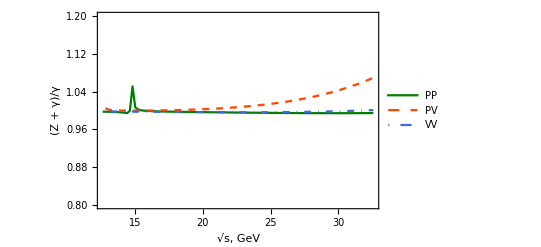

```mathematica
(* Check how Z affects behaviour at LOW energies *)
ListPlot[
(Table[{ecm,(CrossSectionTree["z"<>#]/CrossSectionTree[#])//NNCrossSection},{ecm,$ecmMin,$ecmLowMax,0.2}])&/@AllStates,
PlotRange->{Automatic, {0.8,1.2}},
Frame->True,Joined->True,
FrameLabel->{{"(Z + γ)/γ",""}, {"√s, GeV",""}},
PlotStyle->$PlotStyle3,
PlotLegends->AllStates
]
```

```mathematica
(* Ok. Where tree PP is zero *)
Solve[CrossSectionTree["PP"] == 0,s]//Factor//DeleteDuplicates
```

{{s→4 (MB+MC)^2},{s→(2 (MB+MC)^2 (MB^4+2 MC^4))/(MB MC (MB^2+2 MC^2))}}

```mathematica
tmp=Factor[D[CrossSectionTree["PV"],s]];
Solve[tmp==0,s]
```

{{s→11/2 (MB^2+2 MB MC+MC^2)}}

```mathematica
(√sZeroPP-√sMaxPV)//NN
```

-0.0587155

```mathematica
(* Z contribution at the point where tree PP is zero *)
sZeroPP = (2 (MB+MC)^2 (MB^4+2 MC^4))/(MB MC (MB^2+2 MC^2));
sMaxPV=11/2 (MB^2+2 MB MC+MC^2);
eZeroPP = √sZeroPP;
zContribAtZeroPP = Factor[Factor[CrossSectionTree["zPP"]/.s->sZeroPP]/.SW^2->1-CW^2]//Factor;
(fb zContribAtZeroPP "fb")//NNCrossSection//Chop
```

1.09547×10^-6 fb

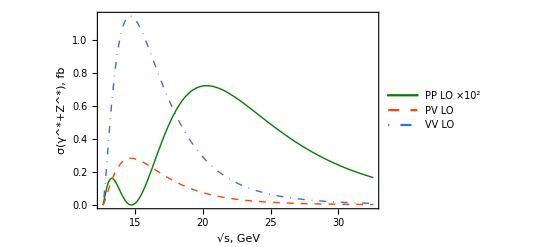

```mathematica
(* Tree level at LOW energies *)
pl = Plot[
{
100 fb CrossSectionTree["zPP"]/.alphaS->AlphaS1LoopMZ[ecm]//NNCrossSection//Evaluate,
fb CrossSectionTree["zPV"]/.alphaS->AlphaS1LoopMZ[ecm]//NNCrossSection//Evaluate,
fb CrossSectionTree["zVV"]/.alphaS->AlphaS1LoopMZ[ecm]//NNCrossSection//Evaluate
},
{ecm,$ecmMin,$ecmLowMax},
Frame->True,
PlotRangePadding->{{0.1,0.1},{0,0.1}},
AxesOrigin->{$ecmMin,0},
PlotStyle->$PlotStyle3,
FrameLabel->{{"σ(γ^*+Z^*), fb",""}, {"√s, GeV",""}},
PlotLegends->{"PP LO ×10^2", "PV LO", "VV LO"},
ImagePadding->{{55,5},{50,5}},
ImageSize->{Automatic,220}
]/.Placed[x___,pos_,r_]:>Placed[x,{0.75,0.75}];
SaveFigure["tree_ecm_low.pdf",pl];
pl
```

```mathematica
(* Check how Z affects behaviour at HIGH energies: in general Z nearly 10 times larger *)
ZtoGamma = (Mean@Table[(CrossSectionTree["z"<>#]/CrossSectionTree[#])//NNCrossSection,
{ecm,$MZ+500,$MZ+600,1}])&/@AllStates//Chop;
Print["ecm : [",$MZ+500," - ", $MZ+600,"] GeV"]
ZtoGamma = Transpose[{("z"<>#<>"/"<>#)&/@AllStates,ZtoGamma}];
Print@TableForm[ZtoGamma]
```

ecm : [591.188 - 691.188] GeV

zPP/PP | 1.53267
zPV/PV | 472.775
zVV/VV | 1.53642

```mathematica
(* Ok. Let's find assymptotic behaviour Z/gamma at E c.m. -> Infinity *)
(* for PV: zPV/PV -> Infinity *)
Series[CrossSectionTree["zPV"]/CrossSectionTree["PV"],{s,Infinity,-1}]
```

(9 (MB^6 MC^2+2 MB^4 MC^4+MB^2 MC^6-4 MB^6 MC^2 SW^2-8 MB^4 MC^4 SW^2-4 MB^2 MC^6 SW^2+8 MB^6 MC^2 SW^4+16 MB^4 MC^4 SW^4+8 MB^2 MC^6 SW^4) s)/(256 CW^4 (MB+MC)^4 (MB^3-2 MC^3)^2 SW^4)+O[1/s]^0

```mathematica
(* for PP and VV: Z/gamma -> constant (the same) *)
Clear[limitZtoGamma];
SWtoCW[x_] := x//.SW^(n_/;EvenQ[n]):>(1-CW^2)^(n/2)
limitZtoGamma[state_]:= Limit[CrossSectionTree["z"<>state]/CrossSectionTree[state],s->Infinity]//SWtoCW//FullSimplify;
Assert[limitZtoGamma["PP"]==limitZtoGamma["VV"]]
limitZtoGamma = limitZtoGamma["PP"];
```

Assert[limitZtoGamma[PP]==limitZtoGamma[VV]]

```mathematica
FullSimplify[limitZtoGamma/.CW->Cos[Subscript[θ, W]]//toR]/.e->√(α 4 π)/.alphaS->Subscript[α, S]/.MB->Subscript[m, b]/.MC->Subscript[m, c]/.MZ->Subscript[m, Z]/.t->Subscript[θ, W]/.GammaZ->Γ/.fBc->Subscript[f, Subscript[B, c]]//TeXForm//CopyToClipboard
```

```mathematica
(* Z/gamma at s->Infinity for PP & VV: *)
limitZtoGamma//NN
```

1.51323

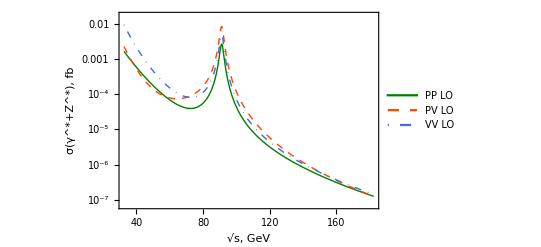

```mathematica
(* Tree level at Z-boson peak *)
pl=
LogPlot[
{
fb CrossSectionTree["zPP"]/.alphaS->AlphaS1LoopMZ[ecm]//NNCrossSection//Evaluate,
fb CrossSectionTree["zPV"]/.alphaS->AlphaS1LoopMZ[ecm]//NNCrossSection//Evaluate,
fb CrossSectionTree["zVV"]/.alphaS->AlphaS1LoopMZ[ecm]//NNCrossSection//Evaluate
},
{ecm,$ecmLowMax,2 $MZ},
FrameTicks->{{Flatten[Table[Table[{n 10^k,If[n==1,Superscript[10,k],""]},{n,1,10}],{k,-7,5}],1],Automatic},{Automatic,Automatic}},
Frame->True,
PlotRange->All,
AxesOrigin->{0,0},
PlotStyle->$PlotStyle3,
FrameLabel->{{"σ(γ^*+Z^*), fb",""}, {"√s, GeV",""}},
PlotLegends->{"PP LO", "PV LO", "VV LO"},
ImagePadding->{{55,5},{50,5}},
ImageSize->{Automatic,220}
]/.Placed[x___,pos_,r_]:>Placed[x,{0.75,0.75}];
SaveFigure["tree_ecm_high.pdf",pl];
pl
```

```mathematica
(CrossSectionTree["zVV"]/CrossSectionTree["zPV"])/.s->MZ^2//NN
(CrossSectionTree["zPV"]/CrossSectionTree["zPP"])/.s->MZ^2//NN
```

0.58002

3.15946

## OneLoop graphics

```mathematica
PickData[data_List,eMin_,eMax_]:=Select[data,eMin≤#[[1]]≤eMax&]
PickNearest[data_List,ecm_,n_:1]:=data[[Nearest[data[[All,1]]->(Range@Length@data),ecm,n]]]

TreeContrib[data_List]:={#[[1]],#[[2,1]]}&/@data;
NLOContrib[data_List]:={#[[1]],#[[2,2]]}&/@data;
NLOTotal[data_List]:={#[[1]],Total[#[[2]]]}&/@data;

SetScale[data_List,OptionsPattern[{ScaleFunc->(#&)}]]:=Module[{tmp = data,func},
func = OptionValue[ScaleFunc];
Do[tmp[[i,2;;]] = tmp[[i,2;;]]/.μR:>func[data[[i,1]]],{i,1,Length[data]}];
tmp
];
SetScaleToEcm[data_List]:=SetScale[data];
SetScaleToFixed[data_List,scale_]:=SetScale[data,ScaleFunc->Function[x,scale]];

ToFemtoBarns[data_List]:=Module[{tmp=data},
If[Length@tmp==0,Return@tmp];
If[Length[tmp[[1]]]==2,
tmp[[All,2]]=fb tmp[[All,2]];,
tmp[[All,{2,3}]]=fb tmp[[All,{2,3}]];
];
Return[tmp]
];
```

Scale dependence for PP at low energies

```mathematica
$VerticalLine[x_,ymin_,ymax_,opts:OptionsPattern[]]:=ListPlot[Table[{x,y},{y,ymin,ymax}],Joined->True,opts]
```

```mathematica
Clear[$PlotScaleDep,$PlotScaleDepFill]
$$delZFromState[state_]:=If[StringTake[state,1]=="z",StringTake[state,2;;],state]
$$cs[state_] :=  ToString[Subscript["σ",$$delZFromState@state],StandardForm];
$$frameLabel[state_] := {{$$cs[state]<>"(s), fb",""}, {"√s, GeV",""}};
$$plotLabel[state_] :=$$cs[state]<>" dependence on μR (α_S is taken at μR as well)";
$$imagePadding = {{65,5},{50,5}};
$$imageSize = {Automatic,220};
$PlotScaleDep[state_,ecmMin_,ecmMax_,OptionsPattern[{MinScale->Function[x,x/2],MaxScale->Function[x,x 2],ScalePoints->10,PlotFunc->ListPlot}]]:=Block[
{alphaS=AlphaS1LoopMZ[μR],fBc=$fBc,minScaleFunc,maxScaleFunc,scaleFuncs={}, scales,func, points, pointsAtMin,pointsAtMax,pointsAtMean},
{minScaleFunc,maxScaleFunc} = OptionValue[#]&/@{MinScale,MaxScale};
Do[
 AppendTo[scaleFuncs,((minScaleFunc[#] + $$i(maxScaleFunc[#]-minScaleFunc[#])/$$scaleDi)&)/.$$i->i/.$$scaleDi->OptionValue[ScalePoints]];
, {i,0,OptionValue[ScalePoints]}];
func = Evaluate[ToFemtoBarns@NLOTotal@PickData[CrossSection[state],ecmMin,ecmMax]];
points = Table[SetScale[func,ScaleFunc->sf],{sf,scaleFuncs}];
{pointsAtMin,pointsAtMax}=SetScale[func,ScaleFunc->#]&/@{minScaleFunc,maxScaleFunc};
pointsAtMean=SetScale[func,ScaleFunc->(((maxScaleFunc[#]+minScaleFunc[#])/2)&)];
scales = Table[sf[2$MC+2$MB],{sf,scaleFuncs}];scales =(Directive[Blue,Opacity[0.8#],Dashing[{#/5,0.1-#/5}]]&/@ √(scales/Max[scales]));
Show[
OptionValue[PlotFunc][points,Joined->True,PlotStyle->scales,PlotRange->All,Frame->True,
FrameLabel->$$frameLabel[state],PlotLabel->$$plotLabel[state],
ImagePadding->$$imagePadding,ImageSize->$$imageSize
],
OptionValue[PlotFunc][{pointsAtMin,pointsAtMean,pointsAtMax},
Joined->True,PlotStyle->{{Black,Thick},{Red,Thick},{Green,Thick}},PlotLegends->{"min scale","mean scale","max scale"}
]
]
]
$PlotScaleDepFill[state_,ecmMin_,ecmMax_,OptionsPattern[{MinScale->Function[x,x/2],MaxScale->Function[x,x 2],ScalePoints->10,PlotFunc->ListPlot}]]:=Block[
{alphaS=AlphaS1LoopMZ[μR],fBc=$fBc,minScaleFunc,maxScaleFunc,scaleFuncs={}, scales,func, points,minTab,maxTab,min,max,all},
{minScaleFunc,maxScaleFunc} = OptionValue[#]&/@{MinScale,MaxScale};
Do[
 AppendTo[scaleFuncs,((minScaleFunc[#] + $$i(maxScaleFunc[#]-minScaleFunc[#])/$$scaleDi)&)/.$$i->i/.$$scaleDi->OptionValue[ScalePoints]];
, {i,0,OptionValue[ScalePoints]}];
func = Evaluate[ToFemtoBarns@NLOTotal@PickData[CrossSection[state],ecmMin,ecmMax]];
points = Table[SetScale[func,ScaleFunc->sf],{sf,scaleFuncs}];
{minTab,maxTab} = Table[ all =points[[All,i]]; all[[ Position[all,#[all[[All,2]]]][[1,1]] ]],{i,1,Length[points[[1]]]}]&/@{Min,Max};
OptionValue[PlotFunc][{minTab,maxTab},
Joined->True,PlotRange->All,Filling->{1->{2}},Frame->True,
PlotStyle->{ConstantArray[{ColorData["HTML","brown"],Opacity[0.7],Thick, Dashed},2]},
FillingStyle->{Directive[Opacity[0.2],Blue]},
FrameLabel->$$frameLabel[state],PlotLabel->$$plotLabel[state],
ImagePadding->$$imagePadding,ImageSize->$$imageSize,
PlotLegends->""
]
]

Clear[$PlotScaleDepForFixedScale,$PlotScaleDepForFixedScaleFill];
$PlotScaleDepForFixedScale[state_,ecmMin_,ecmMax_,opts___] := $PlotScaleDep[state,ecmMin,ecmMax,MinScale->Function[x,$MBc/2],MaxScale->Function[x,4$MBc],opts]
$PlotScaleDepForFixedScaleFill[state_,ecmMin_,ecmMax_,opts___] := $PlotScaleDepFill[state,ecmMin,ecmMax,MinScale->Function[x,$MBc/2],MaxScale->Function[x,4$MBc],opts]
```

```mathematica
(* PP tree + loop cross section (in fb) at the point where it is zero: it is NEGATIVE at all meaningful scales *)
zeroPPNlo = fb Total[PickNearest[CrossSection["zPP"],NN@eZeroPP][[1,2]]]//NNCrossSection//Chop[#,10^-19]&
Quiet[Reduce[zeroPPNlo ≥ 0.0, μR]]
```

-0.000100075+8.16622×10^-7 Log[μR]

μR≥1.66674×10^53

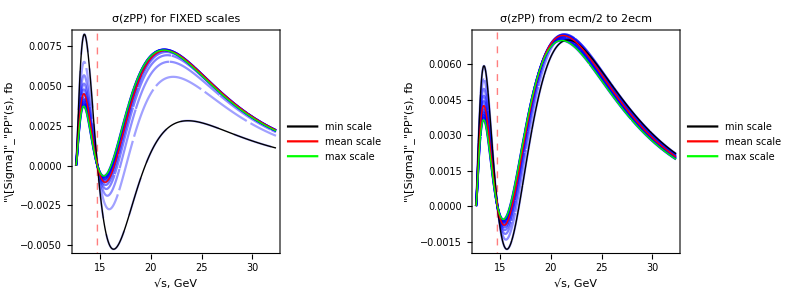

```mathematica
(* Plots for different FIXED scales *)
ppPlotFixed = Show[
$PlotScaleDepForFixedScale["zPP",0,$ecmLowMax],
$VerticalLine[√(sZeroPP//NN),-1,1,PlotStyle->{Red,Thick,Dashed,Opacity[0.5]}]
]/.Placed[x___,pos_,r_]:>Placed[x,{0.78,0.18}];

(* Plots for scales from μR = ecm/2 to μR = 2 ecm *)
ppPlotFloat= Show[
$PlotScaleDep["zPP",0,$ecmLowMax,MinScale->Function[x,x/2],MaxScale->Function[x,2x]],
$VerticalLine[√(sZeroPP//NN),-1,1,PlotStyle->{Red,Thick,Dashed,Opacity[0.5]}]
]/.Placed[x___,pos_,r_]:>Placed[x,{0.75,0.45}];

Grid[{{
ppPlotFixed//Show400//ChangeLabel[#,"σ(zPP) for FIXED scales"]&,
ppPlotFloat//Show400//ChangeLabel[#,"σ(zPP) from ecm/2 to 2ecm"]&
}}]
```

Scale dependence for PV and VV

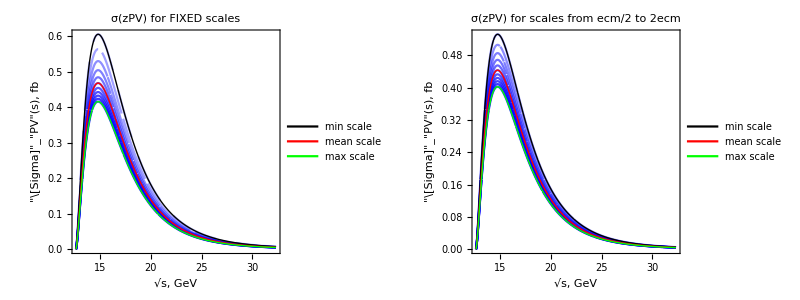

```mathematica
(* for PV *)
Grid[{{
$PlotScaleDepForFixedScale["zPV",0,$ecmLowMax]//Show500//ChangeLabel[#,"σ(zPV) for FIXED scales"]&,
$PlotScaleDep["zPV",0,$ecmLowMax]//Show500//ChangeLabel[#,"σ(zPV) for scales from ecm/2 to 2ecm"]&
}}]/.Placed[x___,pos_,r_]:>Placed[x,{0.75,0.75}]
```

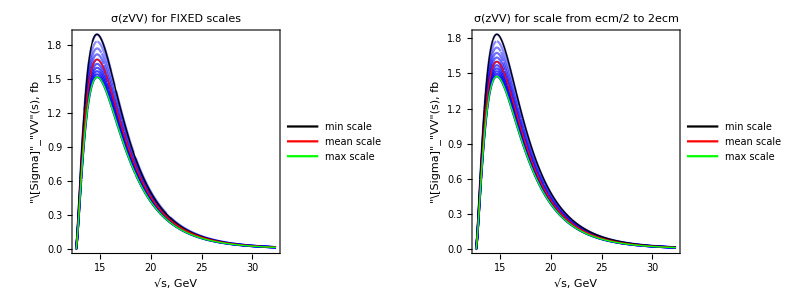

```mathematica
(* for VV *)
Grid[{{
$PlotScaleDepForFixedScale["zVV",0,$ecmLowMax]//Show500//ChangeLabel[#,"σ(zVV) for FIXED scales"]&,
$PlotScaleDep["zVV",0,$ecmLowMax]//Show500//ChangeLabel[#,"σ(zVV) for scale from ecm/2 to 2ecm"]&
}}]/.Placed[x___,pos_,r_]:>Placed[x,{0.75,0.75}]
```

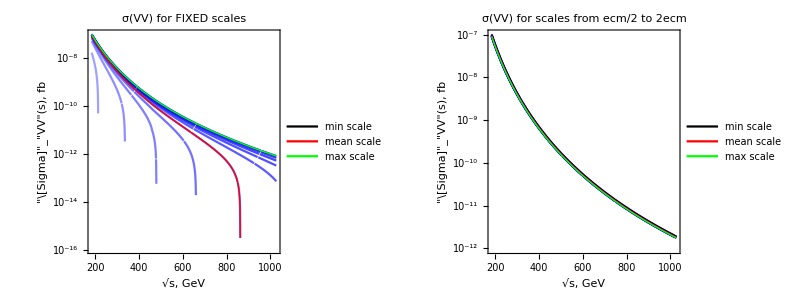

```mathematica
Grid[{{
$PlotScaleDepForFixedScale["VV",2$MZ,100$MZ,PlotFunc->ListLogPlot]//Show500//ChangeLabel[#,"σ(VV) for FIXED scales"]&,
$PlotScaleDep["VV",2$MZ,100$MZ,PlotFunc->ListLogPlot]//Show500//ChangeLabel[#,"σ(VV) for scales from ecm/2 to 2ecm"]&
}}]/.Placed[x___,pos_,r_]:>Placed[x,{0.75,0.75}]
```

Scale dependence for PP, PV and VV: plots

```mathematica
pl = Table[$PlotScaleDepFill[st,0,$ecmLowMax]//ChangeLabel[#,"σ("<>st<>") for scales from ecm/2 to 2ecm"]&,{st,zAllStates}];
pl = pl/.Placed[x___,pos_,r_]:>Placed["√s/2 < μ < 2√s",{0.65,0.35}];
SaveFigure[#[[1]]<>"_oneloop_scale_low.pdf",#[[2]]//RemoveLabel]&/@Transpose[{AllStates,pl}];
```

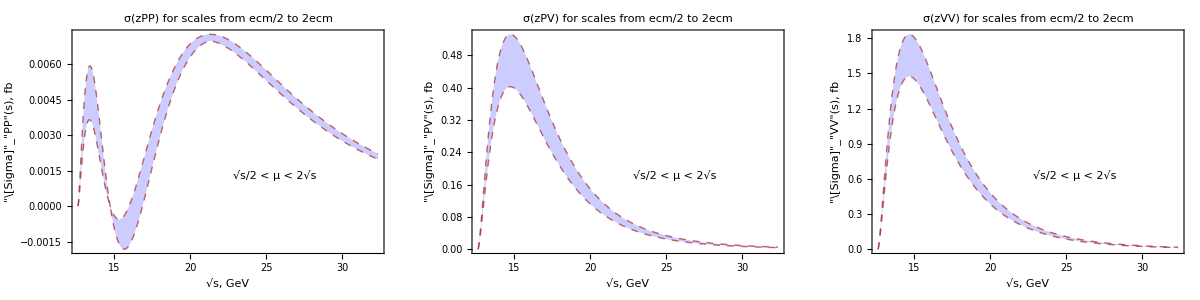

```mathematica
Grid[{pl}]
```

```mathematica
pl = Table[$PlotScaleDepFill[st,$ecmLowMax,2$MZ,PlotFunc->ListLogPlot]//ChangeLabel[#,"σ("<>st<>") for scales from ecm/2 to 2ecm"]&,{st,zAllStates}];
pl = pl/.Placed[x___,pos_,r_]:>Placed["√s/2 < μ < 2√s",{0.35,0.2}];
SaveFigure[#[[1]]<>"_oneloop_scale_high.pdf",#[[2]]//RemoveLabel]&/@Transpose[{AllStates,pl}];
```

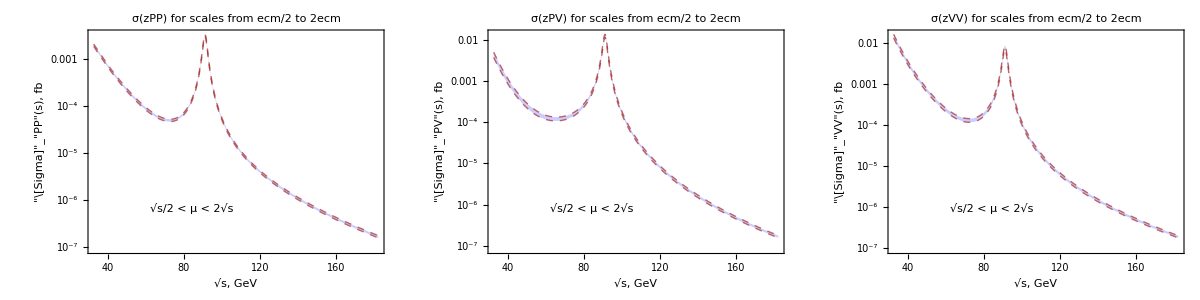

```mathematica
Grid[{pl}]
```

Tree vs loop

```mathematica
Clear[$PlotTreeVsLoop];
$PlotStyle2 = {{Thick,Dashed,ColorData["HTML","orangered"]},{Thick,ColorData["HTML","royalblue"]}};

$PlotTreeVsLoop[state_,ecmMin_,ecmMax_,OptionsPattern[{ScaleFunc->Function[x,x],PlotFunc->ListPlot,KFactorOnly->False,AlphaSFunc->AlphaS1LoopMZ}]]:=Block[
{alphaS=OptionValue[AlphaSFunc][μR],fBc = $fBc,tree,total,opts},

total =PickData[CrossSection[state],ecmMin,ecmMax]//ToFemtoBarns;
total = SetScale[total,ScaleFunc->OptionValue[ScaleFunc]];
tree = TreeContrib@total;
total = NLOTotal@total;

opts = Sequence[Joined->True,Frame->True,PlotStyle->$PlotStyle2,ImagePadding->$$imagePadding,ImageSize->$$imageSize];
If[OptionValue[KFactorOnly],
OptionValue[PlotFunc][Table[{total[[i,1]],total[[i,2]]/tree[[i,2]]},{i,1,Length[total]}],
opts,
FrameLabel-> {{"NLO/LO",""}, {"√s, GeV",""}},
ImagePadding->$$imagePadding,ImageSize->$$imageSize,
PlotLabel->"k-factor ("<>state<>")"
],
OptionValue[PlotFunc][{tree,total},
opts,
FrameLabel->$$frameLabel[state],
PlotLegends->{"LO", "NLO"},
PlotLabel->$$plotLabel[state]
]
]
]
```

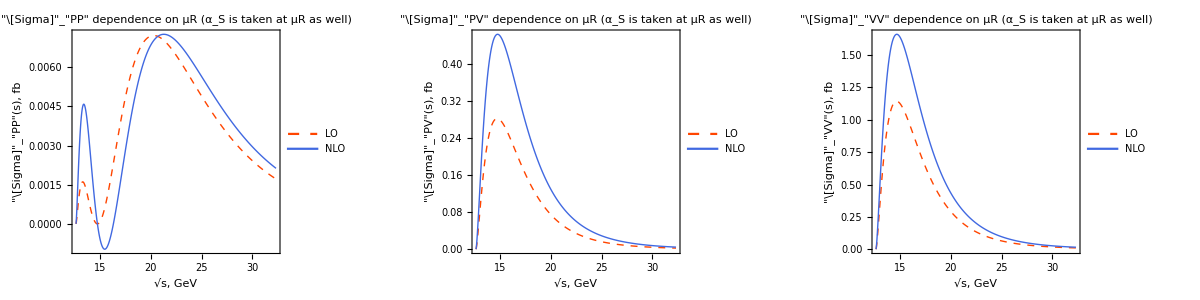

```mathematica
(* Default scale μR = ecm *)
pl = ($PlotTreeVsLoop[#,0,$ecmLowMax])&/@zAllStates/.Placed[x___,pos_,r_]:>Placed[x,{0.8,0.8}];
SaveFigure[#[[1]]<>"_tree_vs_loop_low.pdf",#[[2]]//RemoveLabel]&/@Transpose[{AllStates,pl}];
Grid[{pl}]
```

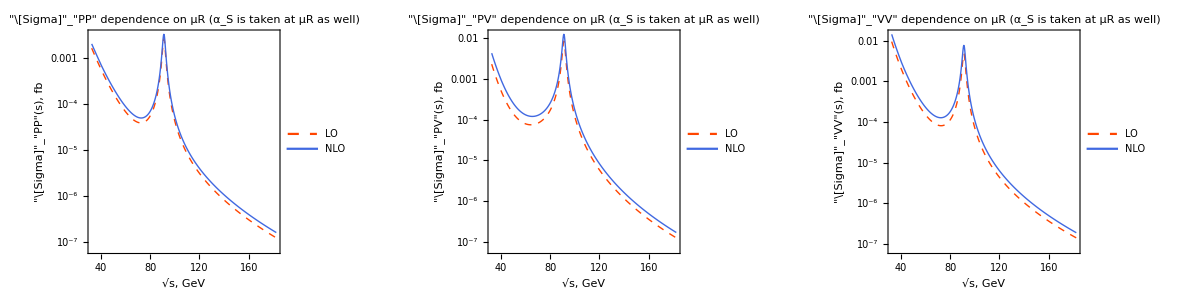

```mathematica
(* Default scale μR = ecm *)
pl = ($PlotTreeVsLoop[#,$ecmLowMax,2$MZ,PlotFunc->ListLogPlot])&/@zAllStates/.Placed[x___,pos_,r_]:>Placed[x,{0.3,0.2}];
SaveFigure[#[[1]]<>"_tree_vs_loop_high.pdf",#[[2]]//RemoveLabel]&/@Transpose[{AllStates,pl}];
Grid[{pl}]
```

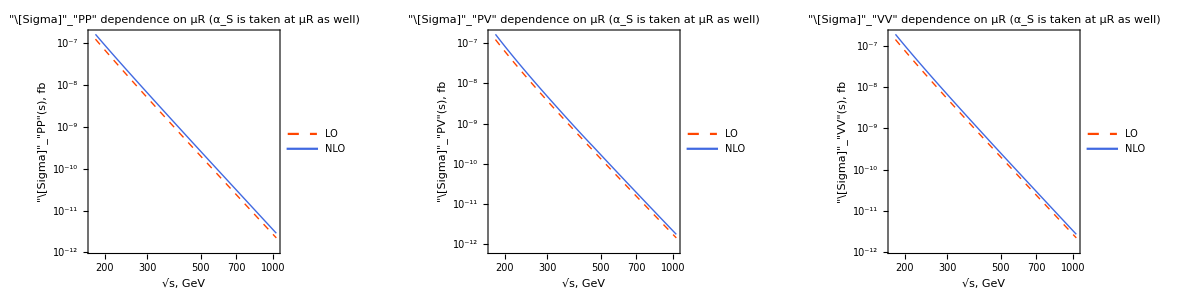

```mathematica
(* Default scale μR = ecm *)
Grid[{
($PlotTreeVsLoop[#,2$MZ,100$MZ,PlotFunc->ListLogLogPlot])&/@zAllStates
}
]/.Placed[x___,pos_,r_]:>Placed[x,{0.8,0.5}]
```

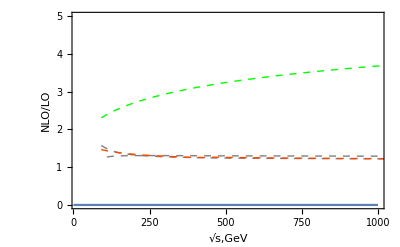

```mathematica
Show[Plot[0,{x,0,1000},PlotRange->{{15,1000},{0,5}},AxesOrigin->{0,0},FrameLabel->{{"NLO/LO",""},{"√s,GeV",""}}],
$PlotTreeVsLoop["zPP",$MZ,100$MZ,PlotFunc->ListPlot,ScaleFunc->Function[x,x],KFactorOnly->True]/.ColorData["HTML","orangered"]->Gray,
$PlotTreeVsLoop["zVV",$MZ,100$MZ,PlotFunc->ListPlot,ScaleFunc->Function[x,x],KFactorOnly->True]/.ColorData["HTML","orangered"]->Gray,
$PlotTreeVsLoop["zPV",$MZ,100$MZ,PlotFunc->ListPlot,ScaleFunc->Function[x,x],KFactorOnly->True],
$PlotTreeVsLoop["PV",$MZ,100$MZ,PlotFunc->ListPlot,ScaleFunc->Function[x,x],KFactorOnly->True]/.ColorData["HTML","orangered"]->Green,
(*The legends in the Epilog are starting here*)Epilog->Inset[Framed[Column[{
LineLegend[{Green},{"   PV Without Z"}],
LineLegend[{Red},{"   PV With Z"}],
LineLegend[{Gray},{"   PP with/without Z"}],
LineLegend[{Gray},{"   VV with/without Z"}]

}],RoundingRadius->5],Scaled[{0.3,0.8}]]
]
```

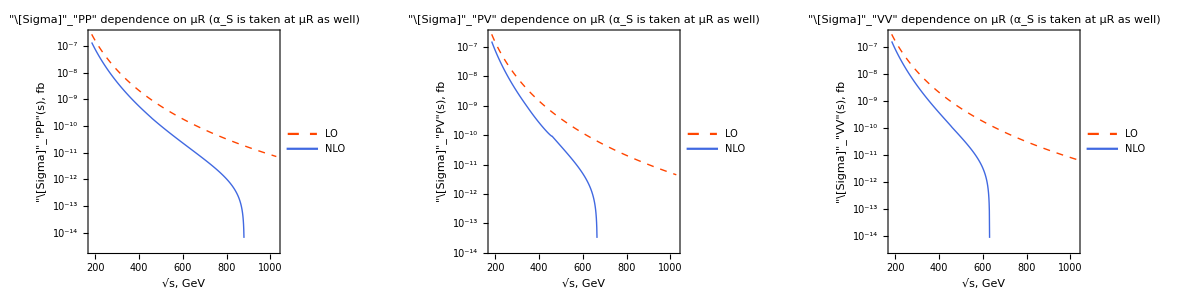

```mathematica
(* For example, what we have for FIXED scale *)
Grid[{
($PlotTreeVsLoop[#,2$MZ,100$MZ,PlotFunc->ListLogPlot,ScaleFunc->Function[x,2$MBc]])&/@zAllStates
}
]/.Placed[x___,pos_,r_]:>Placed[x,{0.8,0.7}]
```

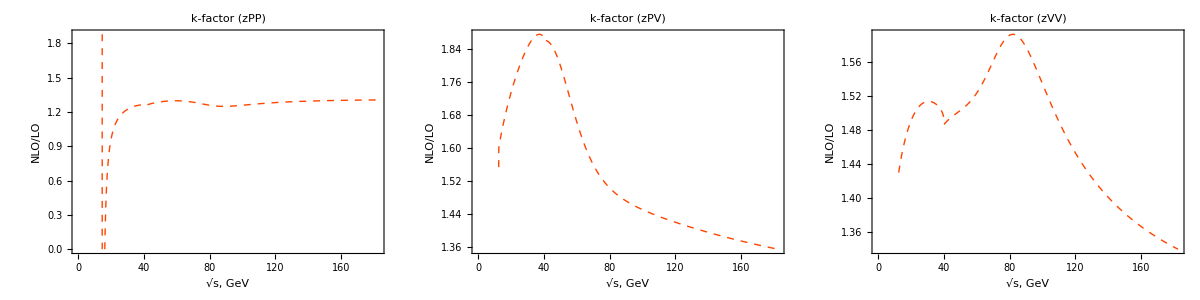

```mathematica
pl = ($PlotTreeVsLoop[#,0,2$MZ,
KFactorOnly->True,
ScaleFunc->Function[x,x ]
(*AlphaSFunc->Function[x,0.3]*)
])&/@zAllStates/.Placed[x___,pos_,r_]:>Placed[x,{0.8,0.8}];
(*SaveFigure[#[[1]]<>"_kfactor_low.pdf",#[[2]]//RemoveLabel]&/@Transpose[{AllStates,pl}];*)
Grid[{pl}]
```

```mathematica
$PlotKFactor[ecmMin_,ecmMax_,OptionsPattern[{ScaleFunc->Function[x,x],AlphaSFunc->AlphaS1LoopMZ,States->zAllStates}]]:=Block[
{alphaS=OptionValue[AlphaSFunc][μR],fBc = $fBc,tree,total,opts},

total =Table[PickData[CrossSection[state],ecmMin,ecmMax]//ToFemtoBarns,{state,OptionValue[States]}];
total = SetScale[#,ScaleFunc->OptionValue[ScaleFunc]]&/@total;
tree = TreeContrib/@total;
total = NLOTotal/@total;

ListPlot[Table[Table[{total[[state,i,1]],total[[state,i,2]]/tree[[state,i,2]]},{i,1,Length[total[[state]]]}],{state,1,3}],
Joined->True,Frame->True,PlotStyle->$PlotStyle3,ImagePadding->$$imagePadding,ImageSize->$$imageSize,
FrameLabel-> {{"σ_NLO/σ_LO",""}, {"√s, GeV",""}},
PlotRange->{{Automatic,Automatic},{0,3}},
ImagePadding->$$imagePadding,ImageSize->$$imageSize,
PlotLegends->{"PP","PV","VV"},
PlotLabel->"k-factor"
]
]
```

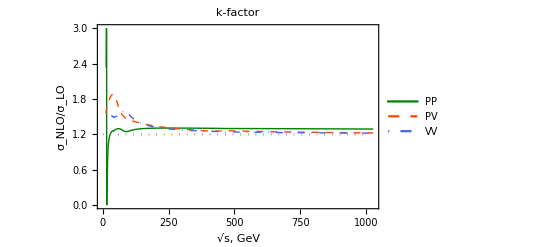

```mathematica
pl = Show[$PlotKFactor[$ecmMin,20$MZ],Plot[1.2,{x,0,1000},PlotStyle->{Gray,Dotted}]]/.Placed[x___,pos_,r_]:>Placed[x,{0.8,0.72}];
SaveFigure["kfactor.pdf",pl//RemoveLabel];
pl
```

```mathematica
PrintScaleTable[point_]:=Block[{nf,fBc=$fBc,alphaS=AlphaS1LoopMZ[μR],ecm,cs,tree,row},
nf[n_] :=ScientificForm[n,2];
Do[
cs = PickNearest[CrossSection[state],point];
{{ecm,cs}} = cs//NLOTotal;
row =((ToString@TeXForm@nf[fb cs/.μR->#])&/@{ecm/2,ecm,2 ecm,2$MBc});
Print["& "<>$$delZFromState@state <>" & $" <>StringRiffle[row,"$ fb & $"]<>"$ fb\\\\"];
,{state,zAllStates}
]
]
```

```mathematica
PrintScaleTable[17]
```

& PP & $3.8\times 10^{-4}$ fb & $1.6\times 10^{-3}$ fb & $2.2\times 10^{-3}$ fb & $1.2\times 10^{-3}$ fb\\

& PV & $3.6\times 10^{-1}$ fb & $3.1\times 10^{-1}$ fb & $2.7\times 10^{-1}$ fb & $3.3\times 10^{-1}$ fb\\

& VV & $1.2$ fb & $1.1$ fb & $9.6\times 10^{-1}$ fb & $1.1$ fb\\

```mathematica
PrintScaleTable[$MZ/2]
```

& PP & $3.9\times 10^{-4}$ fb & $3.7\times 10^{-4}$ fb & $3.5\times 10^{-4}$ fb & $3.9\times 10^{-4}$ fb\\

& PV & $4.8\times 10^{-4}$ fb & $4.2\times 10^{-4}$ fb & $3.7\times 10^{-4}$ fb & $5.5\times 10^{-4}$ fb\\

& VV & $1.4\times 10^{-3}$ fb & $1.3\times 10^{-3}$ fb & $1.2\times 10^{-3}$ fb & $1.5\times 10^{-3}$ fb\\

```mathematica
PrintScaleTable[$MZ]
```

& PP & $3.5\times 10^{-3}$ fb & $3.3\times 10^{-3}$ fb & $3.1\times 10^{-3}$ fb & $3.1\times 10^{-3}$ fb\\

& PV & $1.3\times 10^{-2}$ fb & $1.2\times 10^{-2}$ fb & $1.1\times 10^{-2}$ fb & $1.4\times 10^{-2}$ fb\\

& VV & $8.4\times 10^{-3}$ fb & $7.7\times 10^{-3}$ fb & $6.9\times 10^{-3}$ fb & $9.5\times 10^{-3}$ fb\\

```mathematica
PrintScaleTable[2$MZ]
```

& PP & $1.7\times 10^{-7}$ fb & $1.6\times 10^{-7}$ fb & $1.5\times 10^{-7}$ fb & $1.4\times 10^{-7}$ fb\\

& PV & $1.8\times 10^{-7}$ fb & $1.7\times 10^{-7}$ fb & $1.6\times 10^{-7}$ fb & $1.6\times 10^{-7}$ fb\\

& VV & $2.\times 10^{-7}$ fb & $1.9\times 10^{-7}$ fb & $1.8\times 10^{-7}$ fb & $1.7\times 10^{-7}$ fb\\

## P asymmetry

```mathematica
PAsymmetry[data_]:=Module[{tmp,ecms,treeDsDcos,treeCS,totalDsDcos,totalCS,pickCosPower,calcCoeff,Result},
tmp = data;
ecms = tmp[[All,1]];
treeDsDcos= tmp[[All,2,1]];
totalDsDcos = Total/@tmp[[All,2]];
treeCS =CosIntegrate[treeDsDcos];
totalCS = CosIntegrate[totalDsDcos ];

(*pickCosPower[expr_,pows_]:=Module[{cfs},cfs=CoefficientList[expr,cos];Total[(cfs[[#+1]]cos^#)&/@(pows)]];
pickCosPower[expr_List,pows_]:=pickCosPower[#,pows]&/@expr;
*)
calcCoeff[dsdc_,cs_,cosPow_]:=Transpose[{ecms,CosIntegrate[ dsdc cosPow]/cs}];

Result["Atree"] = calcCoeff[treeDsDcos,treeCS,cos];
Result["Btree"] =  calcCoeff[treeDsDcos,treeCS, cos^2];
Result["Aloop"] = calcCoeff[totalDsDcos,totalCS,cos];
Result["Bloop"] =  calcCoeff[totalDsDcos,totalCS, cos^2];

Return[Result];
]
```

```mathematica
$PlotAsymetry[state_,ecmMin_,ecmMax_,OptionsPattern[{ScaleFunc->Function[x,x],PlotFunc->ListPlot}]]:=Block[
{alphaS=AlphaS1LoopMZ[μR],fBc = $fBc,asym,data,tree,loop},

data =PickData[DsDCosTheta[state],ecmMin,ecmMax];
data = SetScale[data,ScaleFunc->OptionValue[ScaleFunc]];
asym = PAsymmetry[data];
tree = asym["Atree"]//Chop;
loop = asym["Aloop"]//Chop;

OptionValue[PlotFunc][{tree,loop},
Joined->True,
PlotStyle->$PlotStyle2,
Frame->True,
PlotRange->{{$ecmMin+0.5,Automatic},Automatic},
FrameLabel->{{ToString[Subscript[ "<cos θ>",$$delZFromState[state]],StandardForm],""}, {"√s, GeV",""}},
PlotLegends->{"LO", "NLO"},
PlotLabel->"P-asymmetry",
ImagePadding->$$imagePadding,ImageSize->$$imageSize
]
]
```

```mathematica
$MZLine = $VerticalLine[$MZ,-1,1,PlotStyle->{ Dotted,Brown},PlotLegends->{"xx"}]/.Placed[x___,pos_,r_]:>Placed[Rotate[PointLegend[{Directive[None]}, {"MZ"}, LegendMarkers -> {{False,False}}, Joined -> {False}, LabelStyle -> {}, LegendLayout -> "Column"],Pi/2],{0.48,0.05}];
$MZLine = $VerticalLine[$MZ,-1,1,PlotStyle->{ Dotted,Gray}];
```

```mathematica
pl = ($PlotAsymetry[#,0,2$MZ]/.Placed[x___,pos_,r_]:>Placed[x,{0.8,0.6}])&/@zAllStates;
pl = Show[#,$MZLine]&/@pl;
SaveFigure[#[[1]]<>"_asymmetry_ecm.pdf",#[[2]]//RemoveLabel]&/@Transpose[{AllStates,pl}];
```

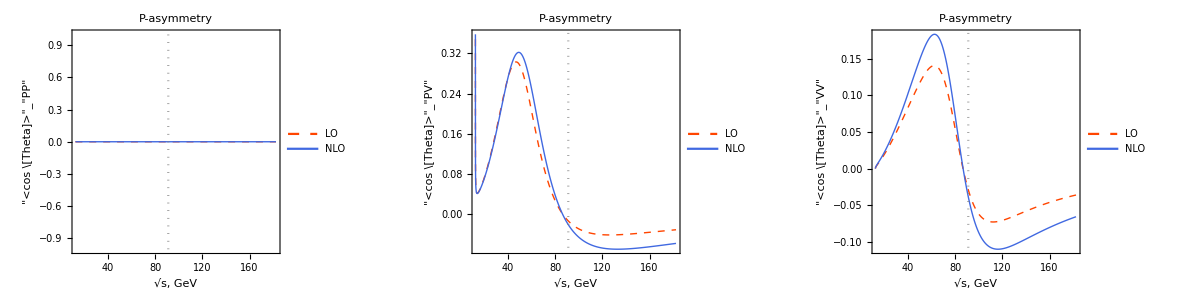

```mathematica
Grid[{pl}]
```

```mathematica
(* Where asymmetry is zero *)
Clear[asym];
(asym[#] = Factor[CosIntegrate[DsDCosThetaTree[#] cos]]//ExpandAll//Factor)&/@zAllStates;
zeroAsymPoint["zPV"] = (8 CW^2 MB^3 MZ^2 SW^2-16 CW^2 MC^3 MZ^2 SW^2)/(3 MB^3-3 MC^3-16 MB^3 SW^2+8 CW^2 MB^3 SW^2+20 MC^3 SW^2-16 CW^2 MC^3 SW^2+16 MB^3 SW^4-32 MC^3 SW^4);
zeroAsymPoint["zVV"] = (8 CW^2 MB^3 MZ^2 SW^2+16 CW^2 MC^3 MZ^2 SW^2)/(3 MB^3+3 MC^3-16 MB^3 SW^2+8 CW^2 MB^3 SW^2-20 MC^3 SW^2+16 CW^2 MC^3 SW^2+16 MB^3 SW^4+32 MC^3 SW^4);
```

```mathematica
FullSimplify[zeroAsymPoint["zVV"]//cw2sin//toR]/.thetaW->Subscript[θ, W]//TeXForm//CopyToClipboard
```

```mathematica
Factor[asym[#]/.s->zeroAsymPoint[#]]&/@zAllStates
```

{0,0,0}

```mathematica
zeroAsymPoint["zVV"]/MZ^2//NN
```

0.904828

```mathematica
zeroAsymPoint["zPV"]/MZ^2//NN
```

0.89694

```mathematica
$PlotDcosTheta[state_,ecm_,OptionsPattern[{ScaleFunc->Function[x,x],PlotFunc->Plot}]]:=Block[
{alphaS=AlphaS1LoopMZ[μR],fBc = $fBc,asym,data,tree,loop},
data =PickNearest[DsDCosTheta[state],ecm][[1]];
data =data[[2]]/.μR->OptionValue[ScaleFunc][data[[1]]];
data = fb data;
tree = data[[1]];
loop =  Total[data];

OptionValue[PlotFunc][{tree,loop},{cos,-1,1},
PlotStyle->$PlotStyle2,
Frame->True,
FrameLabel->{{"d"<>$$cs[state]<>"/dcosθ",""}, {"cos θ",""}},
PlotLegends->{"LO", "NLO"},
PlotLabel->"d"<>$$cs[state]<>"/dcosθ ("<>state<>") at √s = "<>ToString@ecm<>" GeV",
ImagePadding->$$imagePadding,ImageSize->$$imageSize
]
]
```

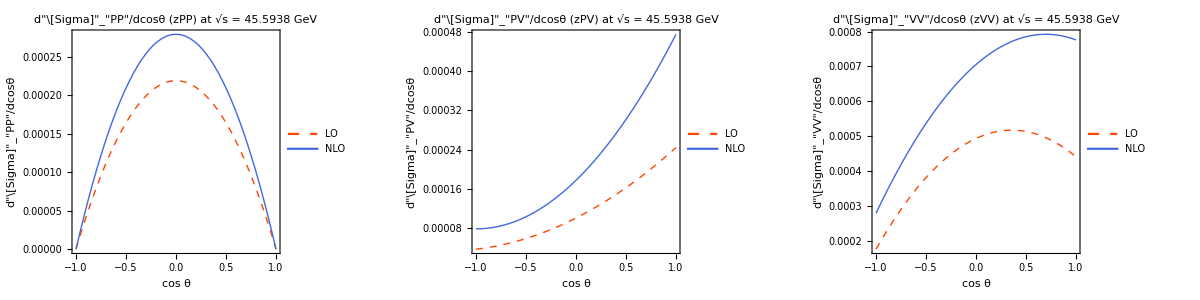

```mathematica
pl = $PlotDcosTheta[#,$MZ/2]&/@zAllStates;
pl = pl/.Placed[x___,pos_,r_]:>Placed[x,{0.2,0.8}];
SaveFigure[#[[1]]<>"_asymmetry_half_mz.pdf",#[[2]]//RemoveLabel]&/@Transpose[{AllStates,pl}];
Grid[{pl}]
```

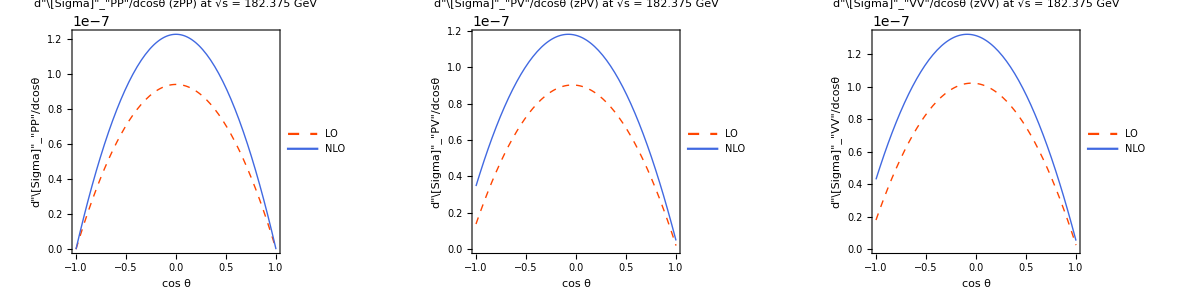

```mathematica
pl = $PlotDcosTheta[#,2$MZ]&/@zAllStates;
pl = pl/.Placed[x___,pos_,r_]:>Placed[x,{0.3,0.2}];
SaveFigure[#[[1]]<>"_asymmetry_two_mz.pdf",#[[2]]//RemoveLabel]&/@Transpose[{AllStates,pl}];
Grid[{pl}]
```

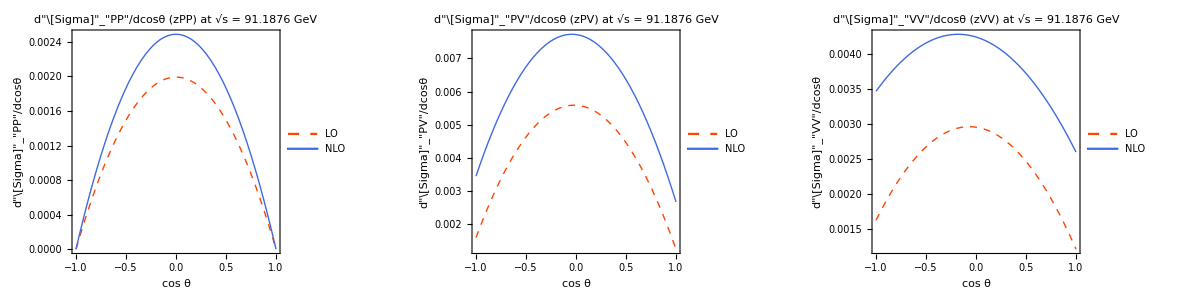

```mathematica
pl = $PlotDcosTheta[#,$MZ]&/@zAllStates;
pl = pl/.Placed[x___,pos_,r_]:>Placed[x,{0.2,0.8}];
SaveFigure[#[[1]]<>"_asymmetry_one_mz.pdf",#[[2]]//RemoveLabel]&/@Transpose[{AllStates,pl}];
Grid[{pl}]
```

## Searching for μR scale

```mathematica
Clear[$PlotMuRDependence]
$PlotMuRDependence[state_,ecm_,from_,to_,di_,OptionsPattern[ShowTicks->False]]:=Block[{alphaS=AlphaS1LoopMZ[ecm],fBc=$fBc,pv, loop,tree,ticks,plot, ticksPlot,NNN},
pv = PickNearest[CrossSection[state],ecm]//ToFemtoBarns;
tree = pv[[1,2,1]];
loop = pv[[1,2,2]];
(*loop = loop/.Log[μR]^2->0;*)
ticks = Range[from,to,di];

plot =Plot[Abs@N[loop/tree],{μR,NN@from-1,NN@to + 1},Frame->True,FrameLabel->{{Subscript["ℛ",$$delZFromState@state],""}, {"μ, GeV",""}},AxesOrigin->{0,0},PlotStyle->Directive[Thick,Black],ImagePadding->$$imagePadding,ImageSize->$$imageSize];
ticksPlot = ListPlot[{},PlotRange->PlotRange[plot],
Frame->True,FrameLabel->{{Subscript["ℛ",$$delZFromState@state],""}, {"μ, GeV","√s = "<>ToString@ecm<>" GeV"}},AxesOrigin->{0,0},FrameTicks->{{Automatic,Automatic},{({#//NN,Style[#,Black,10],{0,0},Directive[Gray,Thick]})&/@ticks,Automatic}}];
If[OptionValue[ShowTicks],
Show[
ticksPlot,
plot,
Sequence@@($VerticalLine[#//NN ,-10,10,PlotStyle->{Opacity[0.5],Gray,Dashed}]&/@ticks),
ListPlot[{{0,0},{1,1},{5,5}},PlotStyle->Black,Ticks->{{{2,Style["x",Gray,12],{0,.02},Directive[Gray,Thick]}},Automatic}]
],
plot
]
]
```

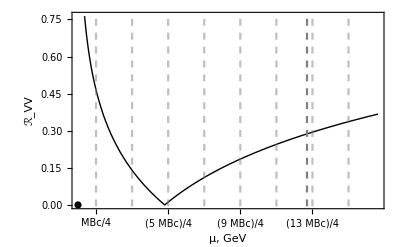

```mathematica
Show[$PlotMuRDependence["zVV",40,MBc/4,4MBc,MBc/2,ShowTicks->True],$VerticalLine[20,-1,20,PlotStyle->{Gray,Dashed}],$VerticalLine[80,-1,20]]
```

```mathematica
$BoundMu[rat_,c_]:=Module[{tmp,a,b,bb},
tmp = CoefficientList[rat,Log[μR]];
If[Length[tmp] ≠ 2, Throw@"Shit."];
a = tmp[[1]];b=tmp[[2]];bb =b/.alphaS->1;
Return@If[bb <0,μR>Exp[(-a+c)/b],0<μR<Exp[(-a+c)/b]];
]
```

```mathematica
tmp =CrossSection["VV"][[2212]];
tmp = Expand[(Factor[tmp[[2,2]]/tmp[[2,1]]]/.fBc->$fBc)/.Log[μR]^2->0]
$BoundMu[tmp,0.5]
```

-12.0876 alphaS+2.22817 alphaS Log[μR]

0<μR<ⅇ^((0.448799 (0.5+12.0876 alphaS))/alphaS)

```mathematica
FindScales[state_,NLOtoLO_,ecmMin_,ecmMax_,OptionsPattern[AlphaS->AlphaS1LoopMZ[μR]]] :=
Block[{alphaS=OptionValue[AlphaS],data, fBc=$fBc,sc,ecm,scales = {}},
data = PickData[CrossSection[state],ecmMin,ecmMax];
Do[
ecm = cs[[1]];
sc = NSolve[cs[[2,2]]/cs[[2,1]]==NLOtoLO&&μR>0&&μR<1000 ecm,μR,Reals];
If[Length[sc]==0,Continue[]];
AppendTo[scales,{ecm,sc[[1,1,2]]}];
,{cs,data}];
Return[scales];
]
```

```mathematica
(*Print@Dynamic@r;
Print@Dynamic@sc;
Clear[scales,scalesData];
Do[
(scalesData[r,#]=FindScales[#,r,19,1000])&/@AllStatesWithZ;
,{r,0,1,0.1}]
Save[ToFileName[$DataPath,"scalesData.m"],scalesData];*)
```

```mathematica
Get[ToFileName[$DataPath,"scalesData.m"]];
```

```mathematica
PlotScalesData[state_,OptionsPattern[{ShowX->True,Show2X->False,MinR->0.1,MaxR->0.5,PlotFunc->ListPlot}]]:=Block[{scales,x,DoTooltip},
scales = OptionValue[PlotFunc][
Table[Tooltip[scalesData[r,state],"z = "<>ToString[NumberForm[r,1]]],{r,OptionValue[MinR],OptionValue[MaxR]+10^-5,0.1}],
Joined->True,PlotStyle->Directive[Gray,Dotted],
PlotRange->If[OptionValue[ShowX],{{50,1000},{50,1000}},{{Automatic,Automatic},{0,Automatic}}],
PlotRangePadding->2.1,
FrameLabel->{{"μ, GeV",""},{"√s, GeV",""}},
ImagePadding->$$imagePadding,ImageSize->$$imageSize
];
x=Plot[If[OptionValue[Show2X],{x/2,x,2x},{x}],{x,0,1000},PlotStyle->Directive[Thick,Black]];
scales =If[OptionValue[ShowX], Show[scales,x],scales];
DoTooltip[data_Tooltip] :=Module[{line},
line=Cases[data,x_Line,Infinity];
line = line[[Ordering[line][[-1]]]];
Return[data/.Tooltip[{___,color_Directive,___},tip_]:>{Text[Style[tip,14],{0,0}+line[[1,If[Length[line[[1]]]>100,-100,-Length[line[[1]]]]]]],color,line}];
];
Return[scales//.x_Tooltip:>DoTooltip[x]]
]
```

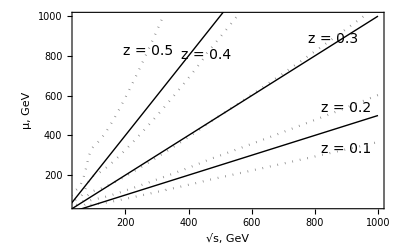
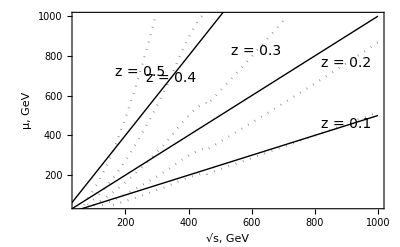
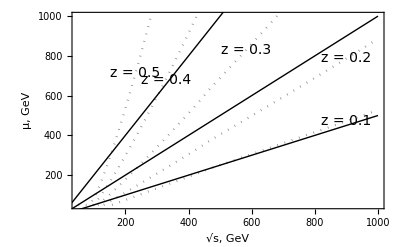

```mathematica
PlotScalesData[#,ShowX->True,Show2X->True]&/@zAllStates
```

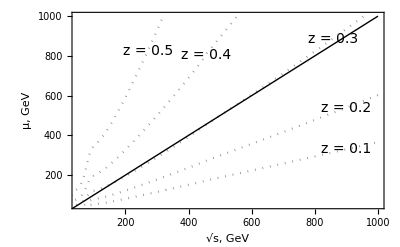

```mathematica
plot = PlotScalesData["zPP",ShowX->True];
SaveFigure["zPP_scales_choice.pdf",plot];
plot
```

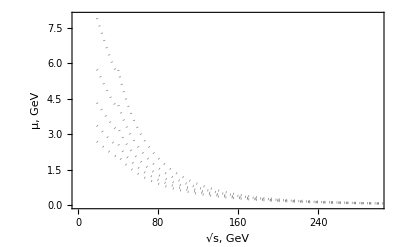

```mathematica
plot = ListPlot[
Table[Tooltip[scalesData[r,"PV"],"r = "<>ToString[NumberForm[r,1]]],{r,0.1,0.5+10^-5,0.1}],
Joined->True,PlotStyle->Directive[Gray,Dotted],
PlotRange->{{0,300},{0,8}},
AxesOrigin->{0,0},
PlotRangePadding->0,
FrameLabel->{{"μ, GeV",""},{"√s, GeV",""}},
ImagePadding->$$imagePadding,ImageSize->$$imageSize
];(*//.{Tooltip[{___,color_Directive,___,line_Line},tip_]:>{Text[Style[tip,14],{0,0}+line[[1,300-Length[line[[1]]]]]],color,line}}*)
SaveFigure["PV_scales_choice.pdf",plot];
plot
```

```mathematica
ScaleUncertainty[state_,ecmMin_,ecmMax_,OptionsPattern[{MinScale->Function[x,x/2],MaxScale->Function[x,x 2],ScalePoints->10,PlotFunc->ListPlot}]]:=Block[{total,tree,nlo,alphaS=AlphaS1LoopMZ[μR],fBc=$fBc,scaleFunc,points,ecm, point,vals},
{minScaleFunc,maxScaleFunc} = OptionValue[#]&/@{MinScale,MaxScale};
total = Evaluate[NLOTotal@PickData[CrossSection[state],ecmMin,ecmMax]];
tree = Evaluate[TreeContrib@PickData[CrossSection[state],ecmMin,ecmMax]];
nlo = Evaluate[NLOContrib@PickData[CrossSection[state],ecmMin,ecmMax]];
points= {};
Do[
ecm =  nlo[[i,1]];
point = nlo[[i,2]];
vals = Table[
Abs[(nlo[[i,2]]/tree[[i,2]])/.μR->minScaleFunc[ecm] + $$i(maxScaleFunc[ecm]-minScaleFunc[ecm])/OptionValue[ScalePoints]], 
{$$i,0,OptionValue[ScalePoints]}
];
AppendTo[points,{ecm,Max[vals]}];,
{i,1,Length[nlo]}
];
Return[points];
]
```

```mathematica
Clear[scaleUncertainty];
(scaleUncertainty[#]=ScaleUncertainty[#,0,1000])&/@AllStatesWithZ;
```

```mathematica
Table[({state,Min[#],Max[#]}&/@{PickData[scaleUncertainty[state],20,1000][[All,2]]}),{state,AllStatesWithZ}]
```

{{{PP,0.226788,0.476542}},{{PV,0.863495,2.73056}},{{VV,0.365251,0.656532}},{{zPP,0.227059,0.447639}},{{zPV,0.340945,0.980971}},{{zVV,0.337392,0.712248}}}

```mathematica
$VerticalArea[x1_,x2_,yMin_,yMax_,opts:OptionsPattern[]]:=
ListPlot[
{
Table[{x1 ,y},{y,yMin,yMax,(yMax-yMin)/100.}],
Table[{x2,y},{y,yMin,yMax,(yMax-yMin)/100.}],
Table[{x,yMin},{x,x1,x2,(x2-x1)/100.}],
Table[{x,yMax},{x,x1,x2,(x2-x1)/100.}]
},
Joined->True,Filling->{4->{3}},
PlotStyle->{Directive[Gray,Dashed],Directive[Gray,Dashed],White,White},
FillingStyle->Directive[Gray,Opacity[0.1]]
]
```

```mathematica
Clear[PlotNLOContrib];
PlotNLOContrib[state_,ecm_,muMin_,muMax_]:=Show[
$PlotMuRDependence[state,ecm,muMin,muMax,(muMax-muMin)/50,ShowTicks->False],
(*$VerticalLine[ecm/2,-1,20,PlotStyle->{Gray,Dashed}],
$VerticalLine[ecm 2,-1,20,PlotStyle->{Gray,Dashed}]*)
$VerticalArea[ecm/2,2ecm,-1,20]
]
```

```mathematica
$PlotMuRDependenceAtFixedEnergy[state_,ecm_,muMin_,muMax_]:=Block[{fBc=$fBc,alphaS=AlphaS1LoopMZ[μR],data,tree,loop,total},
data = PickNearest[CrossSection[state],ecm]//ToFemtoBarns;
tree =(data //TreeContrib)[[1,2]];
total =(data //NLOTotal)[[1,2]];
Show[
Plot[{tree,total},{μR,muMin,muMax},PlotStyle->$PlotStyle2,FrameLabel->{{ToString[Subscript["σ",$$delZFromState@state],StandardForm]<>", fb",""},{"μ, GeV",""}},ImagePadding->$$imagePadding,ImageSize->$$imageSize,PlotLegends->{"LO","NLO"}],
$VerticalArea[ecm/2,2ecm,-1,20]
]/.Placed[x___,pos_,r_]:>Placed[x,{0.5,0.7}]
]
```

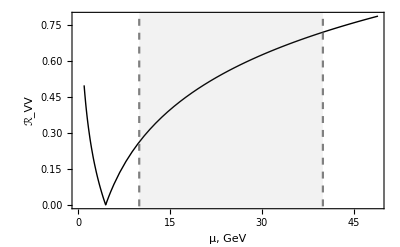

```mathematica
plot = PlotNLOContrib["zVV",20,2,48];
SaveFigure["zVV_scale_dep_at_20.pdf",plot];
plot
```

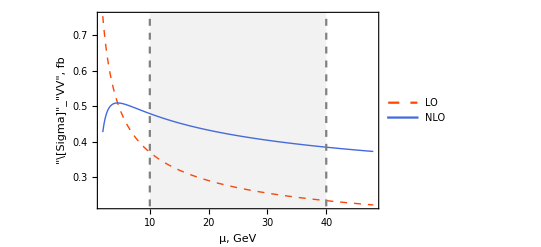

```mathematica
plot = $PlotMuRDependenceAtFixedEnergy["zVV",20,2,48];
SaveFigure["zVV_scale_dep_at_20_tree_loop.pdf",plot];
plot
```

```mathematica
CrossSectionScaleUncertainty[state_,ecmMin_,ecmMax_,order_,OptionsPattern[{MinScale->Function[x,x/2],MaxScale->Function[x,x 2],ScalePoints->10,PlotFunc->ListPlot}]]:=Block[{total,alphaS=AlphaS1LoopMZ[μR],fBc=$fBc,scaleFunc,points,ecm, point,vals},
{minScaleFunc,maxScaleFunc} = OptionValue[#]&/@{MinScale,MaxScale};
total = Evaluate[order@PickData[CrossSection[state],ecmMin,ecmMax]];
points= {};
Do[
ecm =  total[[i,1]];
point = total[[i,2]];
vals = Table[
Abs[point/.μR->minScaleFunc[ecm] + $$i(maxScaleFunc[ecm]-minScaleFunc[ecm])/OptionValue[ScalePoints]], 
{$$i,0,OptionValue[ScalePoints]}
];
AppendTo[points,{ecm,2(Max[vals]-Min[vals])/(Max[vals]+Min[vals])}];,
{i,1,Length[total]}
];
Return[points];
]
```

```mathematica
(#->Mean@CrossSectionScaleUncertainty[#,0,1000,TreeContrib][[All,2]])&/@AllStatesWithZ
```

{PP→0.364292,PV→0.364292,VV→0.364292,zPP→0.364292,zPV→0.364292,zVV→0.364292}

```mathematica
(#->Mean@CrossSectionScaleUncertainty[#,0,1000,NLOTotal][[All,2]])&/@AllStatesWithZ
```

{PP→0.203453,PV→0.300456,VV→0.148378,zPP→0.195617,zPV→0.175639,zVV→0.150974}

$Aborted